```mathematica
(* Tested on v10.4 and 11.1 *)
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

initialization

```mathematica
c=3 10^5(*km/s*);
H0=70(*(km/s)/Mpc*);
Ω=0.32;
```

```mathematica
dP[z_]:=c/H0 NIntegrate[1/Sqrt[Ω (1+t)^3+1-Ω],{t,0,z}](*Proper distance in Mpc*)
dL[z_]:=c (1+z)/H0 NIntegrate[1/Sqrt[Ω (1+t)^3+1-Ω],{t,0,z}](*Luminosity distance in Mpc*)
```

```mathematica
(* for z<0.1, the Hubble law d=cz/H0 gives a distance close to the proper distance, so using size[θ_,z_]:=(θ π c z)/(180 H0) wouldn't actually introduce a big error. Nevertheless: *)
size[θ_,z_]:=θ π/180 dL[z](* θ in degrees; result in Mpc *)
```

```mathematica
filLengthts10Mpc(* [deg] *)=θ/.Table[Solve[size[θ,z]==10,θ][[1]],{z,0.0075,0.1,0.005}]
15 filLengthts10Mpc(* [px] *)
```

{17.7246,10.595,7.53981,5.84272,4.76294,4.01556,3.46763,3.04874,2.71814,2.45062,2.2297,2.04421,1.88626,1.75017,1.6317,1.52764,1.43553,1.35343,1.27978}

{265.869,158.925,113.097,87.6407,71.4441,60.2335,52.0144,45.7311,40.7722,36.7592,33.4455,30.6631,28.294,26.2526,24.4755,22.9147,21.533,20.3014,19.1968}

```mathematica
(*solArc=Solve[Tan[ϕ1]==-Cot[v] (Cos[u] Cos[λ1]+Sin[u] Sin[λ1])&&Tan[ϕ2]==-Cot[v] (Cos[u] Cos[λ2]+Sin[u] Sin[λ2]),{u,v}]//FullSimplify[#,0≤λ1≤2 π&&0≤λ2≤2 π&&-π/2≤ϕ1≤π/2&&-π/2≤ϕ2≤π/2]&*)
```

```mathematica
solArc={{u->ConditionalExpression[ArcTan[(Sin[λ1-λ2] (-Sin[λ2] Tan[ϕ1]+Sin[λ1] Tan[ϕ2]))/(√(-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2)),(Sin[λ1-λ2] (Cos[λ2] Tan[ϕ1]-Cos[λ1] Tan[ϕ2]))/(√(-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2))]+2 π C[1],C[1]∈Integers],v->ConditionalExpression[-ArcTan[(√2)/(√(Csc[λ1-λ2]^2 (-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2)))]+π C[2],C[2]∈Integers]},{u->ConditionalExpression[ArcTan[(Sin[λ1-λ2] (Sin[λ2] Tan[ϕ1]-Sin[λ1] Tan[ϕ2]))/(√(-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2)),(Sin[λ1-λ2] (-Cos[λ2] Tan[ϕ1]+Cos[λ1] Tan[ϕ2]))/(√(-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2))]+2 π C[1],C[1]∈Integers],v->ConditionalExpression[ArcTan[(√2)/(√(Csc[λ1-λ2]^2 (-2+Sec[ϕ1]^2+Sec[ϕ2]^2+Tan[ϕ1]^2-4 Cos[λ1-λ2] Tan[ϕ1] Tan[ϕ2]+Tan[ϕ2]^2)))]+π C[2],C[2]∈Integers]}}/.{C[1]->0,C[2]->0};
```

```mathematica
f[u_,v_,λ_]:=ArcTan[-Cot[v] (Cos[u] Cos[λ]+Sin[u] Sin[λ])]
```

test on mock data

```mathematica
pointsForFit=6;
ridge=30;
localAdaptiveBinarize=20;
deleteSmallComponents=10000;
closing=25;
```

```mathematica
data=Import["mock_data.txt","Table"];
```

```mathematica
Length@data
```

51013

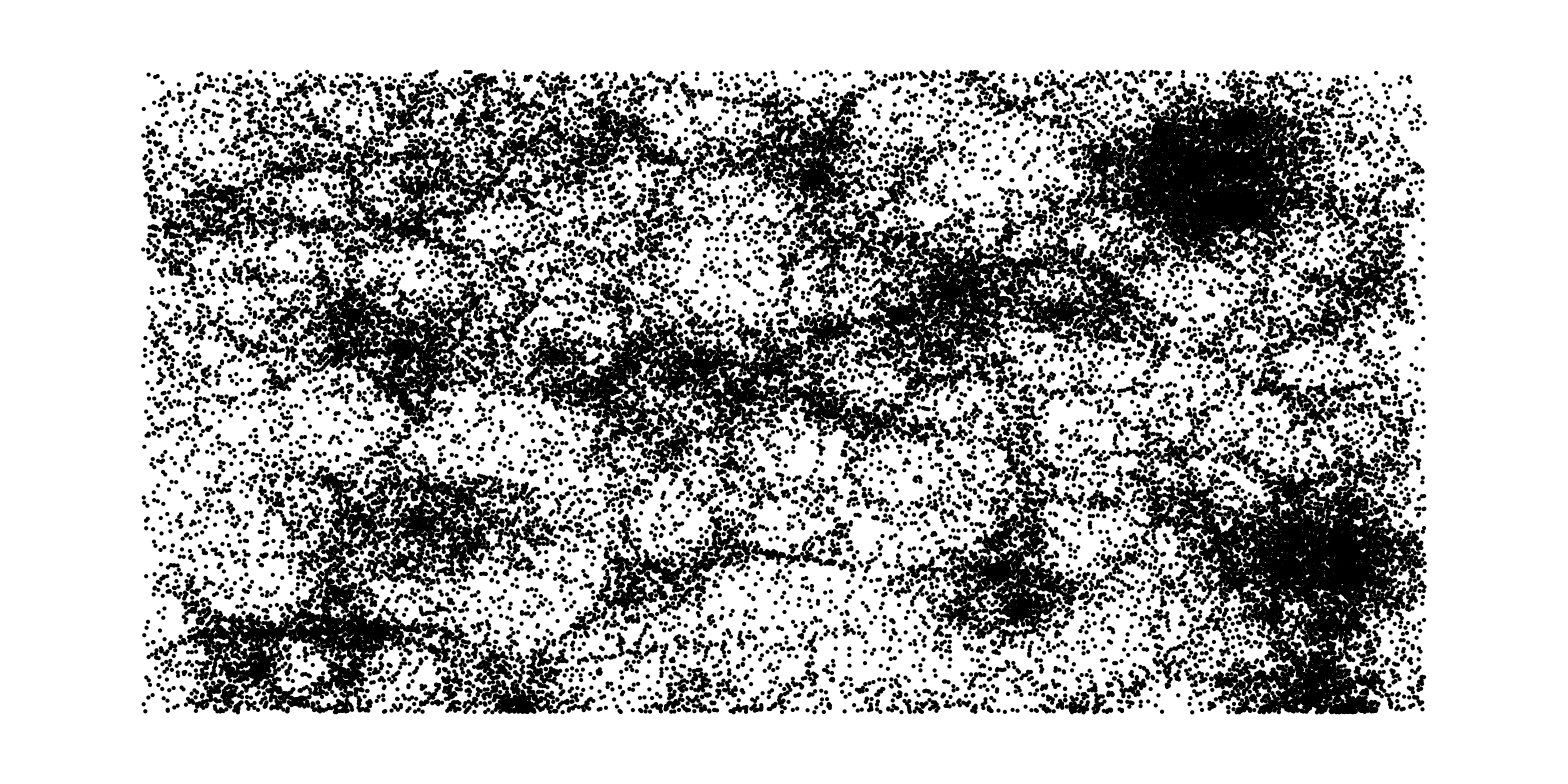

```mathematica
plot=ListPlot[{15 #[[1]],#[[2]]}&/@data,Frame->False,PlotStyle->Directive[Black,PointSize[Tiny]],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None];
plot//Magnify[#,0.5]&//Framed[#,FrameMargins->0]&
```

```mathematica
(img1=ImageAdjust@RidgeFilter[ColorNegate@plot,ridge])//Magnify[#,0.5]&
```

-Graphics-

```mathematica
id=Reverse@ImageData[ColorConvert[img1,"Grayscale"]];
Flatten@id//SmoothHistogram[#,Frame->True,PlotRange->{{0,0.05},All},MaxExtraBandwidths->{0,0},FrameLabel->{"grayscale pixel intensity","PDF"},PlotStyle->Black]&
```

```mathematica
Clear@sm
```

```mathematica
sm[dummy_]=PDF[SmoothKernelDistribution[Flatten@id,MaxExtraBandwidths->{0,0}],dummy]
```

Piecewise[{{InterpolatingFunction[{{0., 1.}}, <>][dummy], 0.≤dummy≤1.}, {0, True}}]

```mathematica
(* scaled by Sqrt[a^2+b^2] distance of {dummy,sm[dummy]} from the straight line *)
Plot[Abs[(sm[0.05]-sm[0.005])/(0.05-0.005) dummy-sm[dummy]+sm[0.005]-0.005 (sm[0.05]-sm[0.005])/(0.05-0.005)],{dummy,0.005,0.05}]
threshold=#[[First[First@Position[#,Max[#[[All,2]]]]],1]]&@({#[[1]],Round[#[[2]],0.1]}&/@Table[{dummy,Abs[(sm[0.05]-sm[0.005])/(0.05-0.005) dummy-sm[dummy]+sm[0.005]-0.005 (sm[0.05]-sm[0.005])/(0.05-0.005)]},{dummy,0.005,0.05,0.0001}])
```

0.0205

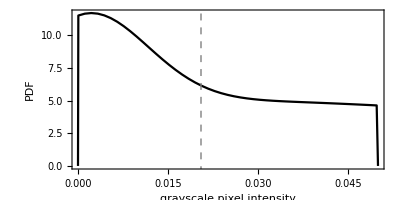

```mathematica
knee=Flatten@id//SmoothHistogram[#,Frame->True,PlotRange->{{0,0.05},All},MaxExtraBandwidths->{0,0},FrameLabel->{"grayscale pixel intensity","PDF"},PlotStyle->Black,Epilog->{Gray,Dashed,Thick,InfiniteLine[{{threshold,0},{threshold,1}}]},AspectRatio->1/2,BaseStyle->4]&
```

```mathematica
id1=Table[UnitStep[id[[i,j]]-threshold],{i,1,Length@id},{j,1,Length@id[[i]]}];
```

```mathematica
binarymap1=Framed[Image@Reverse@id1,FrameMargins->0]//Magnify[#,0.5]&
```

```mathematica
binarymap2=Framed[Image@Reverse@id1//DeleteSmallComponents[#,deleteSmallComponents]&//Closing[#,DiskMatrix@(closing/5)]&,FrameMargins->0]//Magnify[#,0.5]&
```

```mathematica
(highlight=Image@Reverse@id1//DeleteSmallComponents[#,deleteSmallComponents]&//Closing[#,DiskMatrix@(closing/5)]&//Thinning)//Magnify[#,0.5]&
```

-Graphics-

```mathematica
final=HighlightImage[plot,highlight];
range=PlotRange[plot]//Round;
highlightimage=HighlightImage[ListPlot[{15 #[[1]],#[[2]]}&/@data,Frame->False,PlotStyle->Directive[White,PointSize[Tiny]],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None,Background->Transparent],{Cyan,highlight}];
filas=Graphics[{Texture@final,Polygon[Scaled/@{{0,0},{1,0},{1,1},{0,1}},VertexTextureCoordinates->({{0,0},{1,0},{1,1},{0,1}})]},Frame->True,PlotRange->range,AspectRatio->ImageAspectRatio@final,BaseStyle->20,ImageSize->{1800,900},AspectRatio->1/2];
pts=ListPlot[{15 #[[1]],#[[2]]}&/@data,Frame->False,PlotRange->range,DataRange->{15 {8,16},{0,60}},PlotStyle->Directive[Green,Opacity[0.7],PointSize[Tiny]],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None,Background->Transparent];
img4=Show[pts,Prolog->{Inset[img1,Automatic,Automatic,120],Inset[highlightimage,Automatic,Automatic,120]}];
```

```mathematica
i=1;
```

```mathematica
minus=ImageSubtract[highlight, Pruning@highlight];
tails=SelectComponents[minus,"Length",#>15 filLengthts10Mpc[[i]]&];
```

```mathematica
endPoints=PixelValuePositions[Image@MapThread[Boole[#1==1&&#2==2]&,{ImageData[highlight],ListConvolve[BoxMatrix[1],ArrayPad[ImageData[highlight],1]]},2],1];
allPoints=PixelValuePositions[highlight,1];
nf=Nearest[allPoints];
pairs=Sort/@Table[Nearest[endPoints,endPoints[[j]],2],{j,1,Length@endPoints}]//DeleteDuplicates;
```

```mathematica
vec1a=Table[N@First@Differences@pairs[[j]],{j,1,Length@pairs}];
vec1b=-vec1a;
signs1=Table[Sign/@First[Differences@{Last@#,First@#}&@nf[pairs[[j,1]],pointsForFit]],{j,1,Length@pairs}];
signs2=Table[Sign/@First[Differences@{Last@#,First@#}&@nf[pairs[[j,2]],pointsForFit]],{j,1,Length@pairs}];
fit1=Table[LinearModelFit[nf[pairs[[j,1]],pointsForFit],x,x],{j,1,Length@pairs}];
fit2=Table[LinearModelFit[nf[pairs[[j,2]],pointsForFit],x,x],{j,1,Length@pairs}];
vec2a=Table[signs1[[j]] {1,Abs@Normal[fit1[[j]]][[2,1]]},{j,1,Length@fit1}];
vec2b=Table[signs2[[j]] {1,Abs@Normal[fit2[[j]]][[2,1]]},{j,1,Length@fit2}];
pos1=Flatten@Position[#<45&/@Table[Re@ArcCos[Normalize[vec1a[[j]]].Normalize[vec2a[[j]]]] 180/π,{j,1,Length@vec1a}]//Boole,1];
pos2=Flatten@Position[#<45&/@Table[Re@ArcCos[Normalize[vec1b[[j]]].Normalize[vec2b[[j]]]] 180/π,{j,1,Length@vec1b}]//Boole,1];
pos=Intersection[pos1,pos2];
```

```mathematica
coloredTails=Dilation[tails,DiskMatrix[5]]//Colorize[#,ColorRules->{0->Transparent,1->Red}]&//RemoveBackground;
img4withTails=Show[pts,Prolog->Inset[Show[img1,coloredTails,highlightimage],Automatic,Automatic,120]];
```

```mathematica
img4withTails//Magnify[#,0.5]&
```

-Graphics-

```mathematica
ListofEndpoints={Rescale[#[[1]],{1,1800},15 {8.,16.}],Rescale[#[[2]],{1,900},{0.,60.}]}&/@endPoints;
sameLayer=Partition[{Rescale[#[[1]],{1,1800},15 {8.,16.}],Rescale[#[[2]],{1,900},{0.,60.}]}&/@Flatten[pairs[[pos]],1],2,2];
```

```mathematica
uv=Table[{u,v}/.solArc[[1]]/.{λ1->sameLayer[[j,1,1]] Degree,λ2->sameLayer[[j,2,1]] Degree,ϕ1->sameLayer[[j,1,2]] Degree,ϕ2->sameLayer[[j,2,2]] Degree},{j,1,Length@sameLayer}];
connections=Binarize@ColorNegate@(Show@@Table[If[uv[[j,1]]===Indeterminate,ListLinePlot[sameLayer[[j]],Frame->False,PlotStyle->Directive[Black,Thick],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None,PlotRange->{{120,240},{0,60}}],Plot[f[uv[[j,1]],uv[[j,2]],λ Degree] 180/π,{λ,sameLayer[[j,1,1]],sameLayer[[j,2,1]]},Frame->False,PlotStyle->Directive[Black,Thick],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None,PlotRange->{{120,240},{0,60}}]],{j,1,Length@uv}]);
connectionsColor=Dilation[connections,DiskMatrix[5]]//Colorize[#,ColorRules->{0->Transparent,1->Blue}]&//RemoveBackground;
tailsi=Dilation[SelectComponents[ImageSubtract[#,Pruning@#]&@Thinning[ImageAdd[highlight,Binarize@connectionsColor]],"Length",#>15 filLengthts10Mpc[[i]]&],DiskMatrix[5]]//Colorize[#,ColorRules->{0->Transparent,1->If[OddQ@i,Green,Red]}]&;
```

```mathematica
xticks=Table[{x/.Solve[y==120/1799 (x+1798),x][[1]],y},{y,120,240,20}];
yticks=Table[{x/.Solve[y==60/899 (x-1),x][[1]],y},{y,10,60,10}];
img4withTailsandConnections=Show[img1,connections,highlightimage,Epilog->Inset[Show[pts,Frame->True,BaseStyle->40,FrameLabel->{"RA [deg]","DEC [deg]"}]],Frame->True,FrameTicks->{{yticks,Automatic},{xticks,Automatic}},BaseStyle->40,FrameLabel->{"RA [deg]","DEC [deg]"}];
```

```mathematica
pruning=Pruning@ImageAdd[Thinning@connections,highlight];
subMorphh=MorphologicalComponents@DeleteSmallComponents[#,1]&@ImageSubtract[ImageAdd[Thinning@connections,highlight],pruning];
subTails=Table[subMorphh/.x_/;x≠j->0,{j,1,Max@subMorphh}];
tailsCoords=Table[{Rescale[#[[1]],{1,1800},15 {8.,16.}],Rescale[#[[2]],{1,900},{0.,60.}]}&/@PixelValuePositions[Binarize@Image@subTails[[j]],1],{j,1,Length@subTails}];
tailsCoordsOrdered=Table[tailsCoords[[j]][[#]]&/@If[Length@FindCurvePath[tailsCoords[[j]]]==1,First@FindCurvePath[tailsCoords[[j]]],FindHamiltonianPath[Graph@(Join@@(Partition[#,2,1]&/@FindCurvePath[tailsCoords[[j]]]))]],{j,1,Length@tailsCoords}];
tailLengths=Table[Total[Map[ArcCos[Sin[#[[1,2]] Degree] Sin[#[[2,2]] Degree]+Cos[#[[1,2]] Degree] Cos[#[[2,2]] Degree] Cos[(#[[1,1]]-#[[2,1]]) Degree]]&,Partition[tailsCoordsOrdered[[j]],2,2]]] 180/π,{j,1,Length@tailsCoordsOrdered}];
pick=UnitStep[tailLengths-filLengthts10Mpc[[i]]];
finalTails10Mpc=If[MemberQ[pick,1],ImageAdd[Image/@Pick[subTails,pick,1]],ImageAdd[Image/@subTails]];
tailsiFinal=Dilation[finalTails10Mpc,DiskMatrix[5]]//Colorize[#,ColorRules->{0->Transparent,1->If[OddQ@i,Green,Red]}]&;
finalNet=ImageAdd[pruning,finalTails10Mpc];
highlightNet=HighlightImage[ListPlot[{15 #[[1]],#[[2]]}&/@data,Frame->False,PlotStyle->Directive[White,PointSize[Tiny]],ImageSize->{1800,900},AspectRatio->1/2,Axes->False,PlotRangePadding->None,Background->Transparent],{Cyan,finalNet}];
```

```mathematica
intersectionPoints=PixelValuePositions[MorphologicalTransform[Binarize@finalNet,"SkeletonBranchPoints"],1];
ListOfIntersections={Rescale[#[[1]],{1,1800},15 {8.,16.}],Rescale[#[[2]],{1,900},{0.,60.}]}&/@intersectionPoints;
```

```mathematica
(imgFinal=Show[img1,highlightNet,Epilog->Inset[Show[pts,Frame->True,BaseStyle->40,FrameLabel->{"RA [deg]","DEC [deg]"},Epilog->{Orange,PointSize[0.01],Point[ListOfIntersections]}]],Frame->True,FrameTicks->{{yticks,Automatic},{xticks,Automatic}},BaseStyle->40,FrameLabel->{"RA [deg]","DEC [deg]"}])//Magnify[#,1/2]&
```

```mathematica
(imgFinal2=Show[img1,connectionsColor,highlightimage,Epilog->Inset[Show[pts,Frame->True,BaseStyle->50,FrameLabel->{"RA [deg]","DEC [deg]"},LabelStyle->Black,FrameTicksStyle->Black,Epilog->{Orange,PointSize[0.01],Point[ListOfIntersections]}]],Frame->True,FrameTicks->{{yticks,Automatic},{xticks,Automatic}},BaseStyle->50,FrameLabel->{"RA [deg]","DEC [deg]"},LabelStyle->Black,FrameTicksStyle->Black])//Magnify[#,1/2]&
```

-Graphics-

```mathematica
imgdata=Reverse[ImageData[Binarize@finalNet]];
filamLocs={Rescale[#[[1]],{1,1800},15 {8.,16.}],Rescale[#[[2]],{1,900},{0.,60.}]}&/@Select[Flatten[Table[{j,i,imgdata[[i,j]]},{i,1,900},{j,1,1800}],1],#[[3]]==1&][[All,{1,2}]];
```